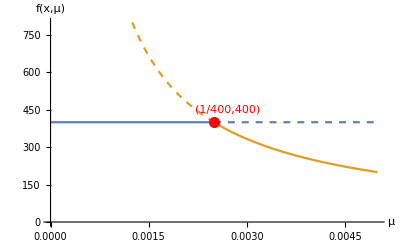

```mathematica
Show[
Plot[{400,1/m},{m,0,1/400},PlotRange->{{0,1/200},{0,800}},PlotStyle->{_,Dashed}],
Plot[{400,1/m},{m,1/400,1/200},PlotRange->{{0,1/200},{0,800}},PlotStyle->{Dashed,_}],
AxesLabel->{"μ","f(x,μ)"},
Epilog->{Red,PointSize[0.02],Point[{1/400,400}],Text["(1/400,400)",{1/370,450}]}
]
```

```mathematica
Solve[
{-dt r Sin[t]+dr Cos[t]==x,dt r Cos[t]+dr Sin[t]==y},{dt,dr}
]//FullSimplify
```

{{dt→1,dr→-6 m^3 r+11 m^2 r^3-6 m r^5+r^7}}

```mathematica
x=-r Sin[t]+r Cos[t](r^2-m)(r^2-2m)(r^2-3m);
y=r Cos[t]+r Sin[t](r^2-m)(r^2-2m)(r^2-3m);
```

```mathematica
Factor[-6 m^3 r+11 m^2 r^3-6 m r^5+r^7]
```

-r (m-r^2) (2 m-r^2) (3 m-r^2)

```mathematica
D[-6 m^3 r+11 m^2 r^3-6 m r^5+r^7,r]//Factor
```

-6 m^3+33 m^2 r^2-30 m r^4+7 r^6

```mathematica
D[-r (m-r^2) (2 m-r^2) (3 m-r^2),r]
```

2 r^2 (m-r^2) (2 m-r^2)+2 r^2 (m-r^2) (3 m-r^2)+2 r^2 (2 m-r^2) (3 m-r^2)-(m-r^2) (2 m-r^2) (3 m-r^2)

```mathematica
d=-6 m^3+33 m^2 r^2-30 m r^4+7 r^6
```

-6 m^3+33 m^2 r^2-30 m r^4+7 r^6

```mathematica
d/.{r->√(3m)}
```

12 m^3

```mathematica
Clear[x]
```

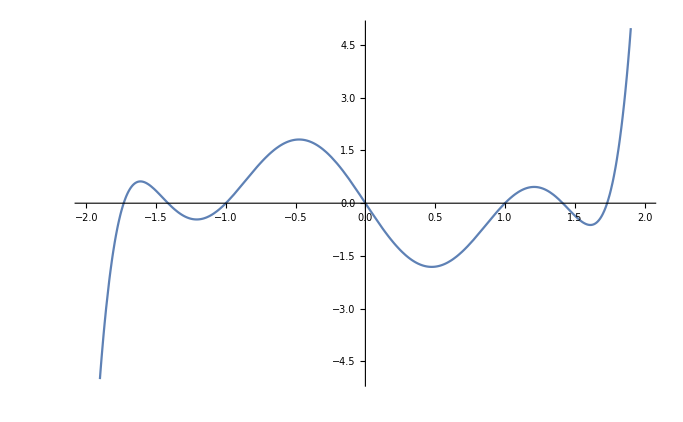

```mathematica
Plot[x(x^2-1)(x^2-2)(x^2-3),{x,-2,2},Ticks->None]
```

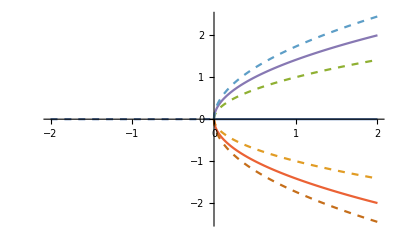

```mathematica
sol=Evaluate[{r}/.Solve[-r (m-r^2) (2 m-r^2) (3 m-r^2)==0,r]];
Show[
Plot[sol,{m,0,2},PlotRange->{{-2,2},All},PlotStyle->{_,Dashed,Dashed,_,_,Dashed,Dashed}],
Plot[sol,{m,-2,0},PlotStyle->Dashed]
]
```

```mathematica
{r}/.Solve[-r (m-r^2) (2 m-r^2) (3 m-r^2)==0,r]
```

{{0},{-√m},{√m},{-√2 √m},{√2 √m},{-√3 √m},{√3 √m}}

```mathematica
Clear[y]
```

```mathematica
Manipulate[
StreamPlot[{-y+x(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m),x+y(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m)},{x,-2,2},{y,-2,2},PlotLabel->m]
,{m,-2,2}]
```

```mathematica
Solve[√(3m)==2,m]
```

{{m→4/3}}

```mathematica
Grad[{-y+x(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m),x+y(x^2+y^2-m)(x^2+y^2-2m)(x^2+y^2-3m)},{x,y}]/.{x->0,y->0}
```

{{-6 m^3,-1},{1,-6 m^3}}

```mathematica
Det[{{-6 m^3,-1},{1,-6 m^3}}-k IdentityMatrix[2]]//Factor
```

1+k^2+12 k m^3+36 m^6

```mathematica
Solve[1+k^2+12 k m^3+36 m^6==0,k]
```

{{k→-ⅈ-6 m^3},{k→ⅈ-6 m^3}}

```mathematica
Grad[{9y+x^3+x y,-x-m y+9y^2},{x,y}]
```

```mathematica
{{3 x^2+y,9+x},{-1,-m+18 y}}/.{x->0,y->0}
```

{{0,9},{-1,-m}}

```mathematica
Det[{{0,9},{-1,-m}}-k IdentityMatrix[2]]//Factor
```

9+k^2+k m

```mathematica
Solve[9+k^2+k m==0,k]
```

{{k→1/2 (-m-√(-36+m^2))},{k→1/2 (-m+√(-36+m^2))}}

```mathematica
px=9r Sin[t]+r^3 Cos[t]^3+r^2 Sin[t]Cos[t];
py=-r Cos[t]-m r Sin[t]+9r^2 Sin[t]^2;
Solve[
{-dt r Sin[t]+dr Cos[t]==px,dt r Cos[t]+dr Sin[t]==py},{dt,dr}
]//FullSimplify//Expand
```

{{dt→-Cos[t]^2-m Cos[t] Sin[t]-r^2 Cos[t]^3 Sin[t]-9 Sin[t]^2+8 r Cos[t] Sin[t]^2,dr→r^3 Cos[t]^4+8 r Cos[t] Sin[t]+r^2 Cos[t]^2 Sin[t]-m r Sin[t]^2+9 r^2 Sin[t]^3}}

```mathematica
NSolve[{9y+x^3+x y==0,-x+0.1y+9y^2==0},{x,y},Reals]
```

{{x→1.66976,y→-0.436322},{x→0.,y→0.}}

```mathematica
Manipulate[
StreamPlot[{9y+x^3+x y,-x-m y+9y^2},{x,-5,5},{y,-5,5},PlotLabel->m,StreamColorFunction->None,StreamPoints->{{{{0.3,0},Red},Automatic}}]
,{{m,0.5},-2,2}]
```

```mathematica
FourierTransform[Cos[x],x,s]
```

√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s]

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamColorFunction->None,StreamPoints->{{{{1,0},Red},{{-1,-1},Green},Automatic}}]
```

```mathematica
Integrate[DiracDelta[-1+s],{s,-2,2}]
```

1

```mathematica
InverseFourierTransform[(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t],s,x]//FullSimplify
```

ⅇ^(-a^2 t) Cos[x]

```mathematica
InverseFourierTransform[f[s],s,x]
```

InverseFourierTransform[f[s],s,x]

```mathematica
Integrate[(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t]Exp[-I s x],{s,-Infinity,+Infinity}]
```

ⅇ^(-a^2 t) √(2 π) Cos[x]

```mathematica
(√(π/2) DiracDelta[-1+s]+√(π/2) DiracDelta[1+s])Exp[-a^2 s^2 t]Exp[-I s x]/.{{s->1},{s->-1}}
```

{ⅇ^(-a^2 t-ⅈ x) √(π/2) DiracDelta[0],ⅇ^(-a^2 t+ⅈ x) √(π/2) DiracDelta[0]}

```mathematica
Total[{ⅇ^(-a^2 t-ⅈ x) √(π/2) DiracDelta[0],ⅇ^(-a^2 t+ⅈ x) √(π/2) DiracDelta[0]}]//FullSimplify
```

```mathematica
ⅇ^(-a^2 t-ⅈ x) √(π/2) +ⅇ^(-a^2 t+ⅈ x) √(π/2) //FullSimplify
```

ⅇ^(-a^2 t) √(2 π) Cos[x]

```mathematica
Det[{{1-m,1},{1,-3-m}}]//Factor
```

-4+2 m+m^2

```mathematica
Eigensystem[{{1,1},{1,-3}}]
```

{{-1-√5,-1+√5},{{2-√5,1},{2+√5,1}}}

```mathematica
I
```

```mathematica
Normalize/@{{2-√5,1},{2+√5,1}}//FullSimplify
```

{{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}

```mathematica
A={{1,1},{1,-3}}
```

{{1,1},{1,-3}}

```mathematica
A.{2-√5,1}
```

{3-√5,-1-√5}

```mathematica
(3-√5)/(2-√5)//FullSimplify
```

-1-√5

```mathematica
B={{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}
```

{{-√(1/2-1/(√5)),√(1/2+1/(√5))},{√(1/2+1/(√5)),1/(√(10+4 √5))}}

```mathematica
Eigenvalues@{{1,1,1},{1,1,0},{1,0,1}}
```

{1+√2,1,1-√2}

```mathematica
Eigenvectors@{{1,1,1},{1,1,0},{1,0,1}}
```

{{√2,1,1},{0,-1,1},{-√2,1,1}}

```mathematica
Det[{{1-m,1,1},{1,1-m,0},{1,0,1-m}}]//Factor
```

```mathematica
Solve[-((-1+m) (-1-2 m+m^2))==0,m]
```

{{m→1},{m→1-√2},{m→1+√2}}

```mathematica
B.A.Transpose@B//FullSimplify
```

{{-1-√5,0},{0,-1+√5}}

```mathematica
(-1+√5)/(-1-√5)//Simplify
```

1/2 (-3+√5)

```mathematica
1/8 D[(x+y)^2-(x-3y)^2,y]/.{y->0}
```

x

```mathematica
PolynomialQuotient[x^5+x^3,x^4+x+1,x]
```

x

```mathematica
PolynomialRemainder[x^5+x^3,x^4+x+1,x]
```

-x-x^2+x^3

```mathematica
(x^2+x+1)(x^5+x^3+1)+(x^2+x)(x^5+x^2+1)//Expand//.{a_Integer->Mod[a,2]}
```

```mathematica
1+2 x+2 x^2+2 x^3+2 x^4+2 x^5+2 x^6+2 x^7//.{a_Integer->Mod[a,2]}
```

1

```mathematica
Eigenvalues[{{1,0,0},{-1,0,1},{-1,-1,2}}]
```

{1,1,1}

```mathematica
Normalize/@Eigenvectors@{{1,1,1},{1,1,0},{1,0,1}}
```

```mathematica
{{0,-1/(√2),1/(√2)},{-1/(√2),1/2,1/2},{1/(√2),1/2,1/2}}
```

```mathematica
P=Transpose@({{0,-1/(√2),1/(√2)},{-1/(√2),1/2,1/2},{1/(√2),1/2,1/2}})
```

{{0,-1/(√2),1/(√2)},{-1/(√2),1/2,1/2},{1/(√2),1/2,1/2}}

```mathematica
Transpose@P.{{1,1,1},{1,1,0},{1,0,1}}.P//Simplify
```

{{1,0,0},{0,1-√2,0},{0,0,1+√2}}

```mathematica
Normalize/@Eigenvectors@{{1,1,1},{1,1,0},{1,0,1}}
```

{{1/(√2),1/2,1/2},{0,-1/(√2),1/(√2)},{-1/(√2),1/2,1/2}}

```mathematica
P.DiagonalMatrix[{1,(1-√2)^4,(1+√2)^4}].Transpose@P//FullSimplify
```

{{17,12,12},{12,9,8},{12,8,9}}

```mathematica
MatrixPower[{{1,1,1},{1,1,0},{1,0,1}},4]
```

{{17,12,12},{12,9,8},{12,8,9}}

```mathematica
A={{2,1,1},{1,2,1},{1,1,2}}
```

{{2,1,1},{1,2,1},{1,1,2}}

```mathematica
Ap.{1/2,-1,1}
```

```mathematica
{3/8,-9/8,7/8}*8/9
```

```mathematica
Ap.{1/3,-1,7/9}
```

```mathematica
{11/36,-37/36,3/4}*36/37
```

```mathematica
Ap.{11/37,-1,27/37}
```

```mathematica
{43/148,-149/148,107/148}/{11/37,-1,27/37}//N
```

{0.977273,1.00676,0.990741}

```mathematica
g
```

```mathematica
{43/149,-1,107/149}//N
```

{0.288591,-1.,0.718121}

```mathematica
149/148//N
```

1.00676

```mathematica
{27/64,-81/64,63/64}*64/81
```

```mathematica
Ap.{1/3,-1,7/9}
```

{11/36,-37/36,3/4}

```mathematica
{1,-1/2,3/2}*2/3
```

{2/3,-1/3,1}

```mathematica
A.{2/3,-1/3,1}
```

```mathematica
{2,1,7/3}*3/7
```

{6/7,3/7,1}

```mathematica
A.{6/7,3/7,1}
```

```mathematica
{22/7,19/7,23/7}/{6/7,3/7,1}//N
```

{3.66667,6.33333,3.28571}

```mathematica
；
```

```mathematica
23/7//N
```

3.28571

```mathematica
Ap=Inverse[{{2,1,1},{1,2,1},{1,1,2}}]
```

{{3/4,-1/4,-1/4},{-1/4,3/4,-1/4},{-1/4,-1/4,3/4}}

```mathematica
pde = D[u[r,θ,t], {t,2}] == 
   ((D[u[r,θ,t], {r,1}] + 
       r D[u[r,θ,t], {r,2}])/
      r + D[u[r,θ,t], {θ,2}]/r^2);
```

```mathematica
ics = u[r, θ, 0] == BesselJ[0,r BesselJZero[0,1]]-0.5BesselJ[0,r BesselJZero[0,3]]&& 
Derivative[0,0,1][u][r, θ, 0] == 0;
```

```mathematica
bcinr=u[1,θ,t]==0;
```

```mathematica
bcsinθ=u[r,0,t]==u[r,2Pi,t];
```

```mathematica
solution=DSolveValue[pde&&ics&&bcinr&&bcsinθ,u[r,θ,t],{r,θ,t}]
```

DSolveValue[u^(0,0,2)[r,θ,t]==(u^(0,2,0)[r,θ,t])/r^2+(u^(1,0,0)[r,θ,t]+r u^(2,0,0)[r,θ,t])/r&&u[r,θ,0]==BesselJ[0,r BesselJZero[0,1]]-0.5 BesselJ[0,r BesselJZero[0,3]]&&u^(0,0,1)[r,θ,0]==0&&u[1,θ,t]==0&&u[r,0,t]==u[r,2 π,t],u[r,θ,t],{r,θ,t}]

```mathematica
BesselJ[0,1]//N
```

0.765198

```mathematica
BesselJZero[0,3]//N
```

8.65373

```mathematica
BesselJZero[0,1]//N
```

2.40483

```mathematica
Table[k,{k,4}]
```

{1,2,3,4}

```mathematica
L=10;
sol=NDSolve[{Laplacian[u[x,y,t],{x,y}]==D[u[x,y,t],{t,2}],u[x,y,0]==0,u[-L,y,t]==u[L,y,t],u[x,-L,t]==u[x,L,t],Derivative[0,0,1][u][x,y,0]==1/2(Erfc[10(x^2+y^2-1)]+1)},u,{x,-L,L},{y,-L,L},{t,0,10},MaxStepSize->0.2]
```

NDSolve::eerr: 警告：t = 10.において独立変数xの方向にスケールされた21.4786の局所空間誤差推定が指定の許容誤差範囲を大きく超えています．100ポイントの格子間隔は，希望の精度または確度を達成するには大きすぎる可能性があります．特異性が形成されたかもしれません．もしくはMaxStepSizeまたはMinPointsメソッドオプションを用いてより小さな格子間隔を指定することができます．

```mathematica
{{u->InterpolatingFunction[{{…, -10., 10., …}, {…, -10., 10., …}, {0., 10.}}, <>]}}du
```

```mathematica
Manipulate[Plot3D[(u[x,y,t]/. First[sol])-t/100,{x,-L/2,L/2},{y,-L/2,L/2},PlotRange->{All,All,{0,3}}],{t,0,10,0.01}]
```

```mathematica
Plot[1/2(Erfc[10(x-1)]+1),{x,-10,10}]
```

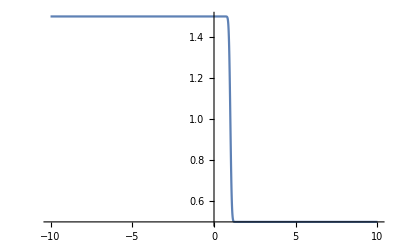

```mathematica
g[t]
```

```mathematica
DSolve[]
```

```mathematica
DSolve[{Laplacian[u[x,y,t],{x,y}]==D[u[x,y,t],{t,2}],u[x,y,0]==0,Derivative[0,0,1][u][x,y,0]==Sin[x]},u,{x,y,t}]
```

DSolve::lpdeprtclr: 指定された線形偏微分方程式の一般解が得られません．特定の解の構築を試みます．

DSolve::bvnul: 一般解の分枝切断線において，与えられた境界条件からは空の解が得られます．

{}

```mathematica
pde = D[u[r,θ,t], {t,2}] == 
   ((D[u[r,θ,t], {r,1}] + 
       r D[u[r,θ,t], {r,2}])/
      r + D[u[r,θ,t], {θ,2}]/r^2);
```

```mathematica
ics = u[r, θ, 0] ==0 && 
Derivative[0,0,1][u][r, θ, 0] == Boole[r<1];
```

```mathematica
bcinr=u[1,θ,t]==0;
```

```mathematica
bcsinθ=bcsinθ = u[r, -π, t] == u[r, π, t] && 
Derivative[0,1,0][u][r, -π, t] == 
Derivative[0,1,0][u][r, π, t];;
```

```mathematica
solution=NDSolve[{pde,u[r, θ, 0] ==0,Derivative[0,0,1][u][r, θ, 0] == Boole[r<1],bcinr,bcsinθ},u[r,θ,t],{r,θ,t}]
```

NDSolve::underdet: 系の従属変数{u[r,-π,t],u[r,π,t],u[r,θ,0],u[r,θ,t],u^(0,0,1)[r,θ,0],u^(0,0,2)[r,θ,t],u^(0,1,0)[r,-π,t],u^(0,1,0)[r,π,t],u^(0,2,0)[r,θ,t]}の数が式の数より多いので，劣決定系です．

NDSolve[{u^(0,0,2)[r,θ,t]==(u^(0,2,0)[r,θ,t])/r^2+(u^(1,0,0)[r,θ,t]+r u^(2,0,0)[r,θ,t])/r,u[r,θ,0]==0,u^(0,0,1)[r,θ,0]==Boole[r<1],u[1,θ,t]==0,u[r,-π,t]==u[r,π,t]&&u^(0,1,0)[r,-π,t]==u^(0,1,0)[r,π,t]},u[r,θ,t],{r,θ,t}]

```mathematica
|
```

```mathematica
pde = r^2 Derivative[0,0,2][u][r, θ, t] == Derivative[0,2,0][u][r, θ, t] + r Derivative[1,0,0][u][r, θ, t] +r^2 Derivative[2,0,0][u][r, θ, t];
```

```mathematica
ics = u[r, θ, 0] ==0 &&Derivative[0,0,1][u][r, θ, 0] == Boole[r<=1];
```

```mathematica
bcinr = Derivative[1,0,0][u][10, θ, t] == 0;
```

```mathematica
bcsinθ = u[r, -π, t] == u[r, π, t] && Derivative[0,1,0][u][r, -π, t] == Derivative[0,1,0][u][r, π, t];
```

```mathematica
solution=DSolveValue[pde&&ics&&bcinr&&bcsinθ,u[r,θ,t],{r,θ,t}]
```

Piecewise[{{t/100+(BesselJ[0,r K[2,0,K[3]]] BesselJ[1,K[2,0,K[3]]] Sin[t K[2,0,K[3]]])/(25 √(BesselJ[0,10 K[2,0,K[3]]]^2+BesselJ[1,10 K[2,0,K[3]]]^2) K[2,0,K[3]]^(3/2) √((BesselJ[0,10 K[2,0,K[3]]]^2+BesselJ[1,10 K[2,0,K[3]]]^2) K[2,0,K[3]]))K[3]1∞, (K[1]|K[3])∈ℤ&&BesselJ[-1+K[1],10 K[2,K[1],K[3]]]==BesselJ[1+K[1],10 K[2,K[1],K[3]]]&&K[1]≥1&&K[3]≥1&&K[2,K[1],K[3]]>0}, {Indeterminate, True}}]

```mathematica
Quiet[eigenvalues=Solve[BesselJ[-1+K[1],K[2,K[1],K[3]]]==BesselJ[0+K[1],K[2,K[1],K[3]]]&&0<K[2,K[1],K[3]]<=157/. K[1]->0,K[2,0,K[3]]]];
```

```mathematica
solution[[1,1,1]]
```

t/100+(BesselJ[0,r K[2,0,K[3]]] BesselJ[1,K[2,0,K[3]]] Sin[t K[2,0,K[3]]])/(25 √(BesselJ[0,10 K[2,0,K[3]]]^2+BesselJ[1,10 K[2,0,K[3]]]^2) K[2,0,K[3]]^(3/2) √((BesselJ[0,10 K[2,0,K[3]]]^2+BesselJ[1,10 K[2,0,K[3]]]^2) K[2,0,K[3]]))K[3]1∞

```mathematica
truncatedangularperiodicwavesolution[r_,θ_,t_]=Chop[N[Plus@@(solution[[1,1,1]]/. eigenvalues)]];
```

```mathematica
Chop[N[truncatedangularperiodicwavesolution[r,θ,t]/. {r->Sqrt[x^2+y^2],θ->ArcTan[x,y]}]]
```

0.5 t+50. (0.04 BesselJ[0,√(x^2+y^2) K[2.,0,K[3.]]] BesselJ[1.,K[2.,0,K[3.]]] Sin[t K[2.,0,K[3.]]])/(√(BesselJ[0,10. K[2.,0,K[3.]]]^2+BesselJ[1.,10. K[2.,0,K[3.]]]^2) K[2.,0,K[3.]]^(3/2) √((BesselJ[0,10. K[2.,0,K[3.]]]^2+BesselJ[1.,10. K[2.,0,K[3.]]]^2) K[2.,0,K[3.]]))K[3.]1.∞

```mathematica
solution[[1,1,1]]/. {K[2,0,K[3]]->BesselJZero[0,n]}//Normal
```

```mathematica
t/100+Sum[(BesselJ[0,r BesselJZero[0,n]] BesselJ[1,BesselJZero[0,n]] Sin[t BesselJZero[0,n]])/(25 √(BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n]^(3/2) √((BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n])),{n,1,20}]/.{r->3,t->2}//N
```

-0.0357908

```mathematica
Plot[t/100+Sum[(BesselJ[0,r BesselJZero[0,n]] BesselJ[1,BesselJZero[0,n]] Sin[t BesselJZero[0,n]])/(25 √(BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n]^(3/2) √((BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n])),{n,1,10}],{t,0,10},{r,0,10}]
```

Plot::nonopt: Plot[t/100+∑_(n=1)^10 (BesselJ[0,r BesselJZero[«2»]] BesselJ[1,BesselJZero[0,n]] Sin[t BesselJZero[«2»]])/(25 √Plus[«2»] BesselJZero[«2»]^Times[«2»] √Times[«2»]),{t,0,10},{r,0,10}]における2の位置より後方にオプションが想定されます（{r,0,10}の代りに）．オプションは規則あるいは規則のリストでなければなりません．

Plot[t/100+∑_(n=1)^10 (BesselJ[0,r BesselJZero[0,n]] BesselJ[1,BesselJZero[0,n]] Sin[t BesselJZero[0,n]])/(25 √(BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n]^(3/2) √((BesselJ[0,10 BesselJZero[0,n]]^2+BesselJ[1,10 BesselJZero[0,n]]^2) BesselJZero[0,n])),{t,0,10},{r,0,10}]

```mathematica
K[2,0,1]
```

K[2,0,1]

```mathematica
Normal[%]
```

```mathematica
Quiet[Manipulate[Block[{$PerformanceGoal="Quality"},Plot3D[Evaluate[Chop[N[truncatedangularperiodicwavesolution[r,θ,t]/. {r->Sqrt[x^2+y^2],θ->ArcTan[x,y]}]]],{x,y}∈Annulus[{0,0},{0.0001,10},{-π,π}],Sequence[PlotRange->{-5,5},PlotTheme->{"Grid"},Ticks->None,Mesh->True,MeshStyle->{Red,Blue},PlotStyle->Hue[0.2],ColorFunction->"TemperatureMap",AxesLabel->Automatic]]],{t,0,10},Sequence[SaveDefinitions->True,ControlPlacement->{Top}]]]
```

```mathematica
150Degree//ToRadicals
```

150 °

```mathematica
N[(150 °)/°]
```

150.

```mathematica
ACACC
```

```mathematica
108/360*2Pi
```

(3 π)/5

```mathematica
D[x Sin[x],x]
```

x Cos[x]+Sin[x]

```mathematica
D[Cos[x]^3,x]
```

-3 Cos[x]^2 Sin[x]

```mathematica
Reduce[{x+y+1==0,x+2y+2==4},{x,y}]
```

x==-4&&y==3

```mathematica
WM3
```

WM3